```mathematica
four=Select[allGraphs5AtomKeys,Length[allGraphs5[#,"vertexsets"]]==4&]
```

{29525,29527,29533,29551,29605,29767,30253,31711,36085,49207}

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

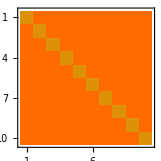

```mathematica
MatrixPlot[
Table[
Table[
Length[
PartitionIntersection[allGraphs5[i,"vertexsets"],allGraphs5[j,"vertexsets"]
]],{i,four}]
,{j,four}
]]
```

```mathematica
four=Select[allGraphs6AtomKeys,Length[allGraphs6[#,"vertexsets"]]==4&]
```

{7174466,7174489,7174537,7174562,7174697,7174726,7174786,7175191,7175263,7175425,7176643,7176667,7176883,7177370,7181015,7181041,7181095,7181746,7183210,7194137,7194139,7194145,7194892,7196404,7200940,7233511,7233583,7233745,7235689,7240063,7253185,7351603,7351627,7351843,7352329,7358161,7371283,7410650,7705895,7705921,7705975,7706623,7708081,7725577,7764946,7883050,8768777,8768779,8768785,8769505,8770963,8775337,8827852,8946004,9300460,11957423,11957425,11957431,11957449,11957503,11957665,12017200,12136756,12495424,13571428}

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

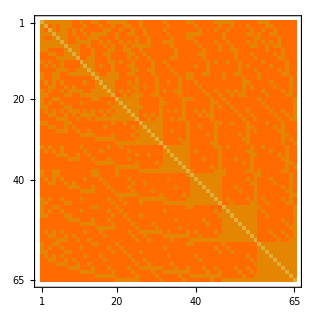

```mathematica
MatrixPlot[
Table[
Table[
Length[
PartitionIntersection[allGraphs6[i,"vertexsets"],allGraphs6[j,"vertexsets"]
]],{i,four}]
,{j,four}
]]
```

```mathematica
MatrixPlot[
Table[
Table[
Length[
PartitionIntersection[allGraphs6[i,"vertexsets"],allGraphs6[j,"vertexsets"]
]],{i,four}]
,{j,four}
],
TableDepth->2,
TableHeadings->{Table[
SymbolToLabel[
 SetsToSymbol[
allGraphs6[i,"vertexsets"]]
],{i,four}]
, Table[
Rotate[SymbolToLabel[
 SetsToSymbol[
allGraphs6[i,"vertexsets"]]
],Pi/2],{i,four}]}
]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

MatrixPlot::optx: Unknown option TableDepth→2 in ….

MatrixPlot[{{4,5,5,5,5,5,5,5,6,6,5,6,6,5,5,6,6,5,5,5,5,5,6,6,6,5,6,6,6,6,6,5,6,6,6,6,6,5,5,6,6,6,6,6,5,5,5,5,5,6,6,6,6,6,6,5,5,5,6,6,6,6,6,6,6},{5,4,6,5,6,5,5,5,6,6,6,5,6,6,6,5,6,6,5,6,6,5,5,6,6,5,6,6,6,6,6,6,5,6,6,6,6,6,6,5,6,6,6,6,6,5,6,6,5,6,6,6,5,6,6,6,6,5,5,6,6,6,6,6,6},{5,6,4,5,6,5,5,6,5,6,5,6,6,6,6,6,5,5,6,6,5,6,6,5,6,6,5,6,6,6,6,5,6,6,6,6,6,6,6,6,5,6,6,6,5,6,6,5,6,6,6,6,6,5,6,6,5,6,6,5,6,6,6,6,6},{5,5,5,4,5,5,5,6,5,6,6,5,6,5,5,5,5,6,6,5,6,6,5,5,6,6,5,6,6,6,6,6,5,6,6,6,6,5,5,5,5,6,6,6,6,6,5,6,6,6,6,6,5,5,6,5,6,6,5,5,6,6,6,6,6},{5,6,6,5,4,5,5,6,6,5,6,6,5,5,5,6,6,6,6,5,6,6,6,6,5,6,6,5,6,6,6,6,6,5,6,6,6,5,5,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,5,5,6,6,6,6,5,6,6,6,6},{5,5,5,5,5,4,5,6,6,5,5,5,5,6,6,5,6,5,6,6,5,6,5,6,5,6,6,5,6,6,6,5,5,5,6,6,6,6,6,5,6,6,6,6,5,6,6,5,6,6,6,6,5,6,5,6,5,6,5,6,5,6,6,6,6},{5,5,5,5,5,5,4,5,5,5,6,6,5,6,6,6,5,6,5,6,6,5,6,5,5,5,5,5,6,6,6,6,6,5,6,6,6,6,6,6,5,6,6,6,6,5,6,6,5,6,6,6,6,5,5,6,6,5,6,5,5,6,6,6,6},{5,5,6,6,6,6,5,4,5,5,6,6,6,5,6,6,6,5,5,6,6,5,5,6,6,5,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,5,6,6,6,5,6,6,5,5,6,6,6,6,6,6,6,5,6,6,6,5,6,6,6},{6,6,5,5,6,6,5,5,4,5,6,6,6,5,6,6,5,5,6,6,6,6,5,5,6,6,5,6,6,6,6,6,6,6,5,6,6,6,6,6,5,5,6,6,6,6,6,6,6,5,6,6,6,5,6,6,6,6,6,5,6,5,6,6,6},{6,6,6,6,5,5,5,5,5,4,6,6,5,5,6,6,6,5,6,6,6,6,5,6,5,6,6,5,6,6,6,6,6,5,5,6,6,6,6,6,6,5,6,6,6,6,6,6,6,5,6,6,6,6,5,6,6,6,6,6,5,5,6,6,6},{5,6,5,6,6,5,6,6,6,6,4,5,5,5,6,6,6,5,5,6,5,6,6,5,6,6,6,6,5,6,6,5,6,6,6,6,6,6,6,6,6,6,5,6,5,6,6,5,6,6,5,6,6,6,6,6,5,6,6,6,6,6,5,6,6},{6,5,6,5,6,5,6,6,6,6,5,4,5,5,6,5,6,6,5,6,6,6,5,5,6,6,6,6,5,6,6,6,5,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,6,6,5,6,5,6,6,6,6,6,5,6,6,6,5,6,6},{6,6,6,6,5,5,5,6,6,5,5,5,4,5,6,6,6,6,5,6,6,6,6,5,5,6,6,5,5,6,6,6,6,5,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,5,6,6,6,5,6,6,6,6,6,5,6,5,6,6},{5,6,6,5,5,6,6,5,5,5,5,5,5,4,5,6,6,5,5,5,6,6,5,5,6,6,6,6,5,6,6,6,6,6,5,6,6,5,5,6,6,5,5,6,6,6,5,6,6,5,5,6,6,6,6,5,6,6,6,6,6,5,5,6,6},{5,6,6,5,5,6,6,6,6,6,6,6,6,5,4,5,5,5,5,5,6,6,6,6,5,6,6,6,6,5,6,6,6,6,6,5,6,5,5,6,6,6,6,6,6,6,5,6,6,6,6,5,6,6,6,5,6,6,6,6,6,6,6,5,6},{6,5,6,5,6,5,6,6,6,6,6,5,6,6,5,4,5,5,5,6,6,6,5,6,5,6,6,6,6,5,6,6,5,6,6,5,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,5,5,6,6,6,6,6,5,6,6,6,6,5,6},{6,6,5,5,6,6,5,6,5,6,6,6,6,6,5,5,4,5,5,6,6,6,6,5,5,6,5,6,6,5,6,6,6,6,6,5,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,5,6,5,6,6,6,6,6,5,6,6,6,5,6},{5,6,5,6,6,5,6,5,5,5,5,6,6,5,5,5,5,4,5,6,5,6,5,6,5,6,6,6,6,5,6,5,6,6,5,5,6,6,6,6,6,5,6,6,5,6,6,5,6,5,6,5,6,6,6,6,5,6,6,6,6,5,6,5,6},{5,5,6,6,6,6,5,5,6,6,5,5,5,5,5,5,5,5,4,6,6,5,6,5,5,5,6,6,5,5,6,6,6,6,6,5,6,6,6,6,6,6,5,6,6,5,6,6,5,6,5,5,6,6,6,6,6,5,6,6,6,6,5,5,6},{5,6,6,5,5,6,6,6,6,6,6,6,6,5,5,6,6,6,6,4,5,5,5,5,5,6,6,6,6,6,5,6,6,6,6,6,5,5,5,6,6,6,6,5,6,6,5,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,5},{5,6,5,6,6,5,6,6,6,6,5,6,6,6,6,6,6,5,6,5,4,5,5,5,5,6,6,6,6,6,5,5,6,6,6,6,5,6,6,6,6,6,6,5,5,6,6,5,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,5},{5,5,6,6,6,6,5,5,6,6,6,6,6,6,6,6,6,6,5,5,5,4,5,5,5,5,6,6,6,6,5,6,6,6,6,6,5,6,6,6,6,6,6,5,6,5,6,6,5,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,5},{6,5,6,5,6,5,6,5,5,5,6,5,6,5,6,5,6,5,6,5,5,5,4,5,5,6,6,6,6,6,5,6,5,6,5,6,5,6,6,5,6,5,6,5,6,6,6,6,6,5,6,6,5,6,6,6,6,6,5,6,6,5,6,6,5},{6,6,5,5,6,6,5,6,5,6,5,5,5,5,6,6,5,6,5,5,5,5,5,4,5,6,5,6,5,6,5,6,6,6,6,6,5,6,6,6,5,6,5,5,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,5,6,6,5,6,5},{6,6,6,6,5,5,5,6,6,5,6,6,5,6,5,5,5,5,5,5,5,5,5,5,4,6,6,5,6,5,5,6,6,5,6,5,5,6,6,6,6,6,6,5,6,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,5,6,6,5,5},{5,5,6,6,6,6,5,5,6,6,6,6,6,6,6,6,6,6,5,6,6,5,6,6,6,4,5,5,5,5,5,6,6,6,6,6,6,5,6,6,6,6,6,6,5,5,6,6,5,6,6,6,5,6,6,6,6,5,6,6,6,5,6,6,6},{6,6,5,5,6,6,5,6,5,6,6,6,6,6,6,6,5,6,6,6,6,6,6,5,6,5,4,5,5,5,5,6,6,6,6,6,6,5,6,6,5,6,6,6,5,6,6,6,6,6,6,6,5,5,6,6,6,6,6,5,6,5,6,6,6},{6,6,6,6,5,5,5,6,6,5,6,6,5,6,6,6,6,6,6,6,6,6,6,6,5,5,5,4,5,5,5,6,6,5,6,6,6,5,6,6,6,6,6,6,5,6,6,6,6,6,6,6,5,6,5,6,6,6,6,6,5,5,6,6,6},{6,6,6,6,6,6,6,6,6,6,5,5,5,5,6,6,6,6,5,6,6,6,6,5,6,5,5,5,4,5,5,6,6,6,6,6,6,5,6,6,6,6,5,6,5,6,6,6,6,6,5,6,5,6,6,6,6,6,6,6,6,5,5,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,6,6,6,6,6,5,5,5,5,5,4,5,6,6,6,6,5,6,5,6,6,6,6,6,6,5,6,6,6,6,6,6,5,5,6,6,6,6,6,6,6,6,5,6,5,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,4,6,6,6,6,6,5,5,6,6,6,6,6,5,5,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,5,6,6,5},{5,6,5,6,6,5,6,6,6,6,5,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,6,6,6,6,6,4,5,5,5,5,5,5,6,6,6,6,6,6,5,5,6,5,6,6,6,6,6,5,6,6,5,6,6,6,6,6,5,6,6},{6,5,6,5,6,5,6,6,6,6,6,5,6,6,6,5,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,5,4,5,5,5,5,5,6,5,6,6,6,6,6,5,6,6,6,6,6,6,5,5,6,6,6,6,5,6,6,6,5,6,6},{6,6,6,6,5,5,5,6,6,5,6,6,5,6,6,6,6,6,6,6,6,6,6,6,5,6,6,5,6,6,6,5,5,4,5,5,5,5,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,5,5,6,6,6,6,6,5,6,5,6,6},{6,6,6,6,6,6,6,5,5,5,6,6,6,5,6,6,6,5,6,6,6,6,5,6,6,6,6,6,6,6,6,5,5,5,4,5,5,5,6,6,6,5,6,6,6,5,6,6,6,5,6,6,6,5,6,6,6,6,6,6,6,5,5,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,6,6,6,6,6,5,6,6,6,6,5,6,5,5,5,5,4,5,5,6,6,6,6,6,6,6,5,6,6,6,6,6,5,6,5,6,6,6,6,6,6,6,6,5,5,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,6,6,6,6,6,5,5,5,5,5,5,4,5,6,6,6,6,6,5,6,5,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,5,6,5},{5,6,6,5,5,6,6,6,6,6,6,6,6,5,5,6,6,6,6,5,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,4,5,6,6,6,6,6,5,5,5,6,6,6,6,6,5,5,6,5,6,6,6,6,6,5,5,6,6},{5,6,6,5,5,6,6,6,6,6,6,6,6,5,5,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,4,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,5,5,6,6,6,6,6,6,6,5,6},{6,5,6,5,6,5,6,6,6,6,6,5,6,6,6,5,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,5,6,6,6,6,6,5,4,5,5,5,5,5,5,6,6,6,6,6,6,5,6,5,6,6,6,5,6,6,6,6,5,6},{6,6,5,5,6,6,5,6,5,6,6,6,6,6,6,6,5,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,6,6,6,6,6,6,5,5,4,5,5,5,5,5,6,6,6,6,6,6,6,5,5,6,6,6,6,5,6,6,6,5,6},{6,6,6,6,6,6,6,5,5,5,6,6,6,5,6,6,6,5,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,5,6,6,6,5,5,5,4,5,5,5,5,6,6,6,5,6,6,6,6,5,6,6,6,6,6,6,5,6,5,6},{6,6,6,6,6,6,6,6,6,6,5,5,5,5,6,6,6,6,5,6,6,6,6,5,6,6,6,6,5,6,6,6,6,6,6,6,6,6,5,5,5,5,4,5,5,5,6,6,6,6,5,6,6,6,5,6,6,6,6,6,6,6,5,5,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,6,6,6,6,6,5,6,6,6,6,6,5,6,5,5,5,5,5,4,5,5,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,5,5},{5,6,5,6,6,5,6,6,6,6,5,6,6,6,6,6,6,5,6,6,5,6,6,6,6,5,5,5,5,5,5,5,6,6,6,6,6,5,5,5,5,5,5,5,4,5,6,5,6,6,6,6,5,6,5,6,5,6,6,6,6,5,6,5,6},{5,5,6,6,6,6,5,5,6,6,6,6,6,6,6,6,6,6,5,6,6,5,6,6,6,5,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,6,6,5,6,6,6,6,5,5,6,6,5,6,6,6,6,5,5,6},{5,6,6,5,5,6,6,6,6,6,6,6,6,5,5,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,6,6,6,6,6,6,6,4,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,5},{5,6,5,6,6,5,6,6,6,6,5,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,5,6,5,4,5,5,5,5,5,5,5,6,5,6,6,6,6,6,6,6,5},{5,5,6,6,6,6,5,5,6,6,6,6,6,6,6,6,6,6,5,6,6,5,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,4,5,5,5,5,5,5,6,6,5,6,6,6,6,6,6,5},{6,6,6,6,6,6,6,5,5,5,6,6,6,5,6,6,6,5,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,5,6,6,6,6,5,5,5,4,5,5,5,5,5,6,6,6,6,6,6,5,6,6,5},{6,6,6,6,6,6,6,6,6,6,5,5,5,5,6,6,6,6,5,6,6,6,6,5,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,5,6,6,6,5,5,5,5,4,5,5,5,5,6,6,6,6,6,6,6,5,6,5},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,6,6,6,6,6,5,6,6,6,6,5,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,4,5,5,5,6,6,6,6,6,6,6,6,5,5},{6,5,6,5,6,5,6,6,6,6,6,5,6,6,6,5,6,6,6,6,6,6,5,6,6,5,5,5,5,5,5,6,5,6,6,6,6,5,6,5,6,6,6,6,5,6,5,5,5,5,5,5,4,5,5,6,6,6,5,6,6,5,6,6,5},{6,6,5,5,6,6,5,6,5,6,6,6,6,6,6,6,5,6,6,6,6,6,6,5,6,6,5,6,6,6,6,5,5,5,5,5,5,5,6,6,5,6,6,6,6,5,5,5,5,5,5,5,5,4,5,6,6,6,6,5,6,6,5,6,5},{6,6,6,6,5,5,5,6,6,5,6,6,5,6,6,6,6,6,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,5,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,6,6,6,6,6,5,6,6,5,5},{5,6,6,5,5,6,6,6,6,6,6,6,6,5,5,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,4,5,5,5,5,5,5,5,5,5},{5,6,5,6,6,5,6,6,6,6,5,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,6,6,5,4,5,5,5,5,5,5,5,5},{5,5,6,6,6,6,5,5,6,6,6,6,6,6,6,6,6,6,5,6,6,5,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,6,5,5,4,5,5,5,5,5,5,5},{6,5,6,5,6,5,6,6,6,6,6,5,6,6,6,5,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,5,6,6,5,5,5,4,5,5,5,5,5,5},{6,6,5,5,6,6,5,6,5,6,6,6,6,6,6,6,5,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,5,6,5,5,5,5,4,5,5,5,5,5},{6,6,6,6,5,5,5,6,6,5,6,6,5,6,6,6,6,6,6,6,6,6,6,6,5,6,6,5,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,4,5,5,5,5},{6,6,6,6,6,6,6,5,5,5,6,6,6,5,6,6,6,5,6,6,6,6,5,6,6,5,5,5,5,5,5,6,6,6,5,6,6,5,6,6,6,5,6,6,5,6,6,6,6,5,6,6,5,6,6,5,5,5,5,5,5,4,5,5,5},{6,6,6,6,6,6,6,6,6,6,5,5,5,5,6,6,6,6,5,6,6,6,6,5,6,6,6,6,5,6,6,5,5,5,5,5,5,5,6,6,6,6,5,6,6,5,6,6,6,6,5,6,6,5,6,5,5,5,5,5,5,5,4,5,5},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,6,6,6,6,6,5,6,6,6,6,5,6,6,6,6,6,5,6,6,5,5,5,5,5,5,5,5,6,6,6,6,6,5,6,6,5,5,5,5,5,5,5,5,5,4,5},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,6,6,6,6,6,5,6,6,6,6,6,5,6,6,6,6,6,6,5,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4}},TableDepth→2,TableHeadings→{{1♁2♁3♁456,1♁2♁36♁45,1♁2♁35♁46,1♁2♁356♁4,1♁2♁34♁56,1♁2♁346♁5,1♁2♁345♁6,1♁26♁3♁45,1♁26♁35♁4,1♁26♁34♁5,1♁25♁3♁46,1♁25♁36♁4,1♁25♁34♁6,1♁256♁3♁4,1♁24♁3♁56,1♁24♁36♁5,1♁24♁35♁6,1♁246♁3♁5,1♁245♁3♁6,1♁23♁4♁56,1♁23♁46♁5,1♁23♁45♁6,1♁236♁4♁5,1♁235♁4♁6,1♁234♁5♁6,16♁2♁3♁45,16♁2♁35♁4,16♁2♁34♁5,16♁25♁3♁4,16♁24♁3♁5,16♁23♁4♁5,15♁2♁3♁46,15♁2♁36♁4,15♁2♁34♁6,15♁26♁3♁4,15♁24♁3♁6,15♁23♁4♁6,156♁2♁3♁4,14♁2♁3♁56,14♁2♁36♁5,14♁2♁35♁6,14♁26♁3♁5,14♁25♁3♁6,14♁23♁5♁6,146♁2♁3♁5,145♁2♁3♁6,13♁2♁4♁56,13♁2♁46♁5,13♁2♁45♁6,13♁26♁4♁5,13♁25♁4♁6,13♁24♁5♁6,136♁2♁4♁5,135♁2♁4♁6,134♁2♁5♁6,12♁3♁4♁56,12♁3♁46♁5,12♁3♁45♁6,12♁36♁4♁5,12♁35♁4♁6,12♁34♁5♁6,126♁3♁4♁5,125♁3♁4♁6,124♁3♁5♁6,123♁4♁5♁6},{1♁2♁3♁456,1♁2♁36♁45,1♁2♁35♁46,1♁2♁356♁4,1♁2♁34♁56,1♁2♁346♁5,1♁2♁345♁6,1♁26♁3♁45,1♁26♁35♁4,1♁26♁34♁5,1♁25♁3♁46,1♁25♁36♁4,1♁25♁34♁6,1♁256♁3♁4,1♁24♁3♁56,1♁24♁36♁5,1♁24♁35♁6,1♁246♁3♁5,1♁245♁3♁6,1♁23♁4♁56,1♁23♁46♁5,1♁23♁45♁6,1♁236♁4♁5,1♁235♁4♁6,1♁234♁5♁6,16♁2♁3♁45,16♁2♁35♁4,16♁2♁34♁5,16♁25♁3♁4,16♁24♁3♁5,16♁23♁4♁5,15♁2♁3♁46,15♁2♁36♁4,15♁2♁34♁6,15♁26♁3♁4,15♁24♁3♁6,15♁23♁4♁6,156♁2♁3♁4,14♁2♁3♁56,14♁2♁36♁5,14♁2♁35♁6,14♁26♁3♁5,14♁25♁3♁6,14♁23♁5♁6,146♁2♁3♁5,145♁2♁3♁6,13♁2♁4♁56,13♁2♁46♁5,13♁2♁45♁6,13♁26♁4♁5,13♁25♁4♁6,13♁24♁5♁6,136♁2♁4♁5,135♁2♁4♁6,134♁2♁5♁6,12♁3♁4♁56,12♁3♁46♁5,12♁3♁45♁6,12♁36♁4♁5,12♁35♁4♁6,12♁34♁5♁6,126♁3♁4♁5,125♁3♁4♁6,124♁3♁5♁6,123♁4♁5♁6}}]

```mathematica
TableForm[
Table[
Table[
SymbolToLabel[
 SetsToSymbol[
PartitionUnion[allGraphs6[i,"vertexsets"],allGraphs6[j,"vertexsets"]
]]
],{i,four}]
,{j,four}
],
TableDepth->2,
TableHeadings->{Table[
SymbolToLabel[
 SetsToSymbol[
allGraphs6[i,"vertexsets"]]
],{i,four}], Table[
SymbolToLabel[
 SetsToSymbol[
allGraphs6[i,"vertexsets"]]
],{i,four}]}
]
```

Symbol::symname: The string "vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

SymbolName::sym: Argument Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]] at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x].

Riffle::list: List expected at position 1 in Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁].

Symbol::symname: The string "vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

SymbolName::sym: Argument Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]] at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x].

Riffle::list: List expected at position 1 in Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁].

Symbol::symname: The string "vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

General::stop: Further output of Symbol::symname will be suppressed during this calculation.

SymbolName::sym: Argument Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]] at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁].

General::stop: Further output of Riffle::list will be suppressed during this calculation.

| 1♁2♁3♁456 | 1♁2♁36♁45 | 1♁2♁35♁46 | 1♁2♁356♁4 | 1♁2♁34♁56 | 1♁2♁346♁5 | 1♁2♁345♁6 | 1♁26♁3♁45 | 1♁26♁35♁4 | 1♁26♁34♁5 | 1♁25♁3♁46 | 1♁25♁36♁4 | 1♁25♁34♁6 | 1♁256♁3♁4 | 1♁24♁3♁56 | 1♁24♁36♁5 | 1♁24♁35♁6 | 1♁246♁3♁5 | 1♁245♁3♁6 | 1♁23♁4♁56 | 1♁23♁46♁5 | 1♁23♁45♁6 | 1♁236♁4♁5 | 1♁235♁4♁6 | 1♁234♁5♁6 | 16♁2♁3♁45 | 16♁2♁35♁4 | 16♁2♁34♁5 | 16♁25♁3♁4 | 16♁24♁3♁5 | 16♁23♁4♁5 | 15♁2♁3♁46 | 15♁2♁36♁4 | 15♁2♁34♁6 | 15♁26♁3♁4 | 15♁24♁3♁6 | 15♁23♁4♁6 | 156♁2♁3♁4 | 14♁2♁3♁56 | 14♁2♁36♁5 | 14♁2♁35♁6 | 14♁26♁3♁5 | 14♁25♁3♁6 | 14♁23♁5♁6 | 146♁2♁3♁5 | 145♁2♁3♁6 | 13♁2♁4♁56 | 13♁2♁46♁5 | 13♁2♁45♁6 | 13♁26♁4♁5 | 13♁25♁4♁6 | 13♁24♁5♁6 | 136♁2♁4♁5 | 135♁2♁4♁6 | 134♁2♁5♁6 | 12♁3♁4♁56 | 12♁3♁46♁5 | 12♁3♁45♁6 | 12♁36♁4♁5 | 12♁35♁4♁6 | 12♁34♁5♁6 | 126♁3♁4♁5 | 125♁3♁4♁6 | 124♁3♁5♁6 | 123♁4♁5♁6
1♁2♁3♁456 | 1♁2♁3♁456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2456♁3 | 1♁23456 | 1♁23456 | 1♁2456♁3 | 1♁23456 | 1♁23456 | 1♁2456♁3 | 1♁2456♁3 | 1♁23456 | 1♁23456 | 1♁2456♁3 | 1♁2456♁3 | 1♁23♁456 | 1♁23♁456 | 1♁23♁456 | 1♁23456 | 1♁23456 | 1♁23456 | 1456♁2♁3 | 13456♁2 | 13456♁2 | 12456♁3 | 12456♁3 | 1456♁23 | 1456♁2♁3 | 13456♁2 | 13456♁2 | 12456♁3 | 12456♁3 | 1456♁23 | 1456♁2♁3 | 1456♁2♁3 | 13456♁2 | 13456♁2 | 12456♁3 | 12456♁3 | 1456♁23 | 1456♁2♁3 | 1456♁2♁3 | 13♁2♁456 | 13♁2♁456 | 13♁2♁456 | 13♁2456 | 13♁2456 | 13♁2456 | 13456♁2 | 13456♁2 | 13456♁2 | 12♁3♁456 | 12♁3♁456 | 12♁3♁456 | 12♁3456 | 12♁3456 | 12♁3456 | 12456♁3 | 12456♁3 | 12456♁3 | 123♁456
1♁2♁36♁45 | 1♁2♁3456 | 1♁2♁36♁45 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁236♁45 | 1♁236♁45 | 1♁23456 | 1♁23456 | 136♁2♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 136♁245 | 136♁245 | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 145♁2♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 1245♁36 | 145♁236 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 145♁2♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 1245♁36 | 145♁236 | 13456♁2 | 145♁2♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 136♁2♁45 | 1236♁45 | 136♁245 | 136♁245 | 136♁2♁45 | 13456♁2 | 13456♁2 | 12♁3456 | 12♁3456 | 12♁36♁45 | 12♁36♁45 | 12♁3456 | 12♁3456 | 1236♁45 | 1245♁36 | 1245♁36 | 1236♁45
1♁2♁35♁46 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁35♁46 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁246♁35 | 1♁246♁35 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁235♁46 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 146♁2♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 146♁235 | 1246♁35 | 146♁235 | 135♁2♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 135♁246 | 135♁246 | 1235♁46 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 146♁2♁35 | 1246♁35 | 146♁235 | 146♁235 | 146♁2♁35 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 135♁2♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 135♁246 | 1235♁46 | 135♁246 | 13456♁2 | 135♁2♁46 | 13456♁2 | 12♁3456 | 12♁35♁46 | 12♁3456 | 12♁3456 | 12♁35♁46 | 12♁3456 | 1246♁35 | 1235♁46 | 1246♁35 | 1235♁46
1♁2♁356♁4 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁356♁4 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁23456 | 1♁2356♁4 | 1♁23456 | 1♁23456 | 1♁2356♁4 | 1♁23456 | 1♁2356♁4 | 1♁24♁356 | 1♁24♁356 | 1♁24♁356 | 1♁23456 | 1♁23456 | 1♁2356♁4 | 1♁23456 | 1♁23456 | 1♁2356♁4 | 1♁2356♁4 | 1♁23456 | 13456♁2 | 1356♁2♁4 | 13456♁2 | 12356♁4 | 1356♁24 | 12356♁4 | 13456♁2 | 1356♁2♁4 | 13456♁2 | 12356♁4 | 1356♁24 | 12356♁4 | 1356♁2♁4 | 14♁2♁356 | 14♁2♁356 | 14♁2♁356 | 14♁2356 | 14♁2356 | 14♁2356 | 13456♁2 | 13456♁2 | 1356♁2♁4 | 13456♁2 | 13456♁2 | 12356♁4 | 12356♁4 | 1356♁24 | 1356♁2♁4 | 1356♁2♁4 | 13456♁2 | 12♁356♁4 | 12♁3456 | 12♁3456 | 12♁356♁4 | 12♁356♁4 | 12♁3456 | 12356♁4 | 12356♁4 | 124♁356 | 12356♁4
1♁2♁34♁56 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁34♁56 | 1♁2♁3456 | 1♁2♁3456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁256♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁256♁34 | 1♁256♁34 | 1♁234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁23456 | 1♁234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁23456 | 1♁234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 156♁2♁34 | 1256♁34 | 156♁234 | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 156♁2♁34 | 1256♁34 | 156♁234 | 156♁234 | 156♁2♁34 | 134♁2♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 134♁256 | 134♁256 | 1234♁56 | 13456♁2 | 13456♁2 | 134♁2♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 134♁256 | 134♁256 | 1234♁56 | 13456♁2 | 13456♁2 | 134♁2♁56 | 12♁34♁56 | 12♁3456 | 12♁3456 | 12♁3456 | 12♁3456 | 12♁34♁56 | 1256♁34 | 1256♁34 | 1234♁56 | 1234♁56
1♁2♁346♁5 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁346♁5 | 1♁2♁3456 | 1♁23456 | 1♁23456 | 1♁2346♁5 | 1♁25♁346 | 1♁25♁346 | 1♁25♁346 | 1♁23456 | 1♁23456 | 1♁2346♁5 | 1♁23456 | 1♁2346♁5 | 1♁23456 | 1♁23456 | 1♁2346♁5 | 1♁23456 | 1♁2346♁5 | 1♁23456 | 1♁2346♁5 | 13456♁2 | 13456♁2 | 1346♁2♁5 | 1346♁25 | 12346♁5 | 12346♁5 | 15♁2♁346 | 15♁2♁346 | 15♁2♁346 | 15♁2346 | 15♁2346 | 15♁2346 | 13456♁2 | 13456♁2 | 1346♁2♁5 | 13456♁2 | 12346♁5 | 1346♁25 | 12346♁5 | 1346♁2♁5 | 13456♁2 | 13456♁2 | 1346♁2♁5 | 13456♁2 | 12346♁5 | 1346♁25 | 12346♁5 | 1346♁2♁5 | 13456♁2 | 1346♁2♁5 | 12♁3456 | 12♁346♁5 | 12♁3456 | 12♁346♁5 | 12♁3456 | 12♁346♁5 | 12346♁5 | 125♁346 | 12346♁5 | 12346♁5
1♁2♁345♁6 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁3456 | 1♁2♁345♁6 | 1♁26♁345 | 1♁26♁345 | 1♁26♁345 | 1♁23456 | 1♁23456 | 1♁2345♁6 | 1♁23456 | 1♁23456 | 1♁23456 | 1♁2345♁6 | 1♁23456 | 1♁2345♁6 | 1♁23456 | 1♁23456 | 1♁2345♁6 | 1♁23456 | 1♁2345♁6 | 1♁2345♁6 | 16♁2♁345 | 16♁2♁345 | 16♁2♁345 | 16♁2345 | 16♁2345 | 16♁2345 | 13456♁2 | 13456♁2 | 1345♁2♁6 | 1345♁26 | 12345♁6 | 12345♁6 | 13456♁2 | 13456♁2 | 13456♁2 | 1345♁2♁6 | 1345♁26 | 12345♁6 | 12345♁6 | 13456♁2 | 1345♁2♁6 | 13456♁2 | 13456♁2 | 1345♁2♁6 | 1345♁26 | 12345♁6 | 12345♁6 | 13456♁2 | 1345♁2♁6 | 1345♁2♁6 | 12♁3456 | 12♁3456 | 12♁345♁6 | 12♁3456 | 12♁345♁6 | 12♁345♁6 | 126♁345 | 12345♁6 | 12345♁6 | 12345♁6
1♁26♁3♁45 | 1♁2456♁3 | 1♁236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁26♁345 | 1♁26♁3♁45 | 1♁26♁345 | 1♁26♁345 | 1♁2456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2456♁3 | 1♁2456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2456♁3 | 1♁2456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁236♁45 | 1♁236♁45 | 1♁23456 | 1♁23456 | 126♁3♁45 | 126♁345 | 126♁345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 1345♁26 | 145♁26♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 12456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 1345♁26 | 145♁26♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 12456♁3 | 145♁26♁3 | 13♁2456 | 13♁2456 | 13♁26♁45 | 13♁26♁45 | 13♁2456 | 13♁2456 | 1236♁45 | 1345♁26 | 1345♁26 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 126♁3♁45 | 1236♁45 | 126♁345 | 126♁345 | 126♁3♁45 | 12456♁3 | 12456♁3 | 1236♁45
1♁26♁35♁4 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁246♁35 | 1♁2356♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁26♁345 | 1♁26♁345 | 1♁26♁35♁4 | 1♁26♁345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2356♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2356♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁246♁35 | 1♁246♁35 | 1♁23456 | 1♁2356♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2356♁4 | 1♁2356♁4 | 1♁23456 | 126♁345 | 126♁35♁4 | 126♁345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 135♁246 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1345♁26 | 135♁26♁4 | 135♁246 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 12356♁4 | 14♁2356 | 14♁2356 | 14♁26♁35 | 14♁26♁35 | 14♁2356 | 14♁2356 | 1246♁35 | 1345♁26 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 135♁246 | 1345♁26 | 135♁26♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 135♁246 | 12356♁4 | 135♁26♁4 | 1345♁26 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1246♁35 | 126♁345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 126♁35♁4 | 126♁345 | 126♁35♁4 | 12356♁4 | 1246♁35 | 12356♁4
1♁26♁34♁5 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁256♁34 | 1♁2346♁5 | 1♁26♁345 | 1♁26♁345 | 1♁26♁345 | 1♁26♁34♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁256♁34 | 1♁256♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | 1♁23456 | 1♁2346♁5 | 126♁345 | 126♁345 | 126♁34♁5 | 1256♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 15♁2346 | 15♁2346 | 15♁26♁34 | 15♁26♁34 | 15♁2346 | 15♁2346 | 1256♁34 | 134♁256 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1345♁26 | 134♁26♁5 | 134♁256 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1345♁26 | 134♁256 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1345♁26 | 134♁26♁5 | 134♁256 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1345♁26 | 134♁26♁5 | 1256♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 126♁345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 126♁345 | 126♁34♁5 | 126♁34♁5 | 1256♁34 | 12346♁5 | 12346♁5
1♁25♁3♁46 | 1♁2456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁235♁46 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁25♁346 | 1♁23456 | 1♁2456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁25♁3♁46 | 1♁25♁346 | 1♁25♁346 | 1♁2456♁3 | 1♁2456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2456♁3 | 1♁2456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁235♁46 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 146♁235 | 1346♁25 | 146♁25♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 146♁235 | 125♁3♁46 | 125♁346 | 125♁346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1235♁46 | 12456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1346♁25 | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 146♁25♁3 | 146♁235 | 146♁25♁3 | 12456♁3 | 13♁2456 | 13♁25♁46 | 13♁2456 | 13♁2456 | 13♁25♁46 | 13♁2456 | 1346♁25 | 1235♁46 | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 125♁3♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 125♁346 | 1235♁46 | 125♁346 | 12456♁3 | 125♁3♁46 | 12456♁3 | 1235♁46
1♁25♁36♁4 | 1♁23456 | 1♁245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2356♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁25♁346 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2356♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁25♁346 | 1♁25♁36♁4 | 1♁25♁346 | 1♁2356♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁245♁36 | 1♁2356♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2356♁4 | 1♁2356♁4 | 1♁23456 | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1346♁25 | 136♁25♁4 | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 125♁346 | 125♁36♁4 | 125♁346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 12356♁4 | 14♁2356 | 14♁25♁36 | 14♁2356 | 14♁2356 | 14♁25♁36 | 14♁2356 | 1346♁25 | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1346♁25 | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 136♁25♁4 | 136♁245 | 136♁25♁4 | 12356♁4 | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 125♁346 | 1245♁36 | 125♁36♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 125♁346 | 12356♁4 | 125♁36♁4 | 1245♁36 | 12356♁4
1♁25♁34♁6 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁256♁34 | 1♁25♁346 | 1♁2345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁256♁34 | 1♁25♁346 | 1♁25♁346 | 1♁25♁34♁6 | 1♁256♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2345♁6 | 1♁23456 | 1♁2345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2345♁6 | 1♁23456 | 1♁2345♁6 | 1♁2345♁6 | 16♁2345 | 16♁2345 | 16♁25♁34 | 16♁25♁34 | 16♁2345 | 16♁2345 | 125♁346 | 125♁346 | 125♁34♁6 | 1256♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1256♁34 | 134♁256 | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 134♁256 | 134♁25♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1346♁25 | 12345♁6 | 134♁256 | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 134♁256 | 134♁25♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1346♁25 | 12345♁6 | 134♁25♁6 | 1256♁34 | 125♁346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 125♁346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 125♁34♁6 | 1256♁34 | 125♁34♁6 | 12345♁6 | 12345♁6
1♁256♁3♁4 | 1♁2456♁3 | 1♁23456 | 1♁23456 | 1♁2356♁4 | 1♁256♁34 | 1♁23456 | 1♁23456 | 1♁2456♁3 | 1♁2356♁4 | 1♁256♁34 | 1♁2456♁3 | 1♁2356♁4 | 1♁256♁34 | 1♁256♁3♁4 | 1♁2456♁3 | 1♁23456 | 1♁23456 | 1♁2456♁3 | 1♁2456♁3 | 1♁2356♁4 | 1♁23456 | 1♁23456 | 1♁2356♁4 | 1♁2356♁4 | 1♁23456 | 12456♁3 | 12356♁4 | 1256♁34 | 1256♁3♁4 | 12456♁3 | 12356♁4 | 12456♁3 | 12356♁4 | 1256♁34 | 1256♁3♁4 | 12456♁3 | 12356♁4 | 1256♁3♁4 | 14♁256♁3 | 14♁2356 | 14♁2356 | 14♁256♁3 | 14♁256♁3 | 14♁2356 | 12456♁3 | 12456♁3 | 13♁256♁4 | 13♁2456 | 13♁2456 | 13♁256♁4 | 13♁256♁4 | 13♁2456 | 12356♁4 | 12356♁4 | 134♁256 | 1256♁3♁4 | 12456♁3 | 12456♁3 | 12356♁4 | 12356♁4 | 1256♁34 | 1256♁3♁4 | 1256♁3♁4 | 12456♁3 | 12356♁4
1♁24♁3♁56 | 1♁2456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 4, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁24♁356 | 1♁234♁56 | 1♁23456 | 1♁23456 | 1♁2456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2456♁3 | 1♁24♁3♁56 | 1♁24♁356 | 1♁24♁356 | 1♁2456♁3 | 1♁2456♁3 | 1♁234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁23456 | 1♁234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1356♁24 | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 156♁24♁3 | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1356♁24 | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 156♁24♁3 | 156♁234 | 156♁24♁3 | 124♁3♁56 | 124♁356 | 124♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1234♁56 | 12456♁3 | 12456♁3 | 13♁24♁56 | 13♁2456 | 13♁2456 | 13♁2456 | 13♁2456 | 13♁24♁56 | 1356♁24 | 1356♁24 | 1234♁56 | 124♁3♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 124♁356 | 124♁356 | 1234♁56 | 12456♁3 | 12456♁3 | 124♁3♁56 | 1234♁56
1♁24♁36♁5 | 1♁23456 | 1♁245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁24♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁24♁356 | 1♁24♁36♁5 | 1♁24♁356 | 1♁2346♁5 | 1♁245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | 1♁23456 | 1♁2346♁5 | 136♁245 | 1356♁24 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 136♁245 | 136♁24♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 15♁2346 | 15♁24♁36 | 15♁2346 | 15♁2346 | 15♁24♁36 | 15♁2346 | 1356♁24 | 124♁356 | 124♁36♁5 | 124♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1245♁36 | 1356♁24 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 136♁245 | 136♁24♁5 | 136♁24♁5 | 1356♁24 | 12346♁5 | 124♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1245♁36 | 124♁36♁5 | 124♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1245♁36 | 124♁36♁5 | 12346♁5
1♁24♁35♁6 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁246♁35 | 1♁24♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁2345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2345♁6 | 1♁23456 | 1♁24♁356 | 1♁24♁356 | 1♁24♁35♁6 | 1♁246♁35 | 1♁2345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2345♁6 | 1♁23456 | 1♁2345♁6 | 1♁2345♁6 | 16♁2345 | 16♁24♁35 | 16♁2345 | 16♁2345 | 16♁24♁35 | 16♁2345 | 135♁246 | 1356♁24 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 135♁246 | 135♁24♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1356♁24 | 124♁356 | 124♁356 | 124♁35♁6 | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1246♁35 | 12345♁6 | 1356♁24 | 135♁246 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 135♁246 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 135♁24♁6 | 1356♁24 | 135♁24♁6 | 12345♁6 | 124♁356 | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 124♁356 | 124♁35♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1246♁35 | 12345♁6 | 124♁35♁6 | 12345♁6
1♁246♁3♁5 | 1♁2456♁3 | 1♁23456 | 1♁246♁35 | 1♁23456 | 1♁23456 | 1♁2346♁5 | 1♁23456 | 1♁2456♁3 | 1♁246♁35 | 1♁2346♁5 | 1♁2456♁3 | 1♁23456 | 1♁23456 | 1♁2456♁3 | 1♁2456♁3 | 1♁2346♁5 | 1♁246♁35 | 1♁246♁3♁5 | 1♁2456♁3 | 1♁23456 | 1♁2346♁5 | 1♁23456 | 1♁2346♁5 | 1♁23456 | 1♁2346♁5 | 12456♁3 | 1246♁35 | 12346♁5 | 12456♁3 | 1246♁3♁5 | 12346♁5 | 15♁246♁3 | 15♁2346 | 15♁2346 | 15♁246♁3 | 15♁246♁3 | 15♁2346 | 12456♁3 | 12456♁3 | 12346♁5 | 1246♁35 | 1246♁3♁5 | 12456♁3 | 12346♁5 | 1246♁3♁5 | 12456♁3 | 13♁2456 | 13♁246♁5 | 13♁2456 | 13♁246♁5 | 13♁2456 | 13♁246♁5 | 12346♁5 | 135♁246 | 12346♁5 | 12456♁3 | 1246♁3♁5 | 12456♁3 | 12346♁5 | 1246♁35 | 12346♁5 | 1246♁3♁5 | 12456♁3 | 1246♁3♁5 | 12346♁5
1♁245♁3♁6 | 1♁2456♁3 | 1♁245♁36 | 1♁23456 | 1♁23456 | 1♁23456 | 1♁23456 | 1♁2345♁6 | 1♁2456♁3 | 1♁23456 | 1♁23456 | 1♁2456♁3 | 1♁245♁36 | 1♁2345♁6 | 1♁2456♁3 | 1♁2456♁3 | 1♁245♁36 | 1♁2345♁6 | 1♁2456♁3 | 1♁245♁3♁6 | 1♁23456 | 1♁23456 | 1♁2345♁6 | 1♁23456 | 1♁2345♁6 | 1♁2345♁6 | 16♁245♁3 | 16♁2345 | 16♁2345 | 16♁245♁3 | 16♁245♁3 | 16♁2345 | 12456♁3 | 1245♁36 | 12345♁6 | 12456♁3 | 1245♁3♁6 | 12345♁6 | 12456♁3 | 12456♁3 | 1245♁36 | 12345♁6 | 12456♁3 | 1245♁3♁6 | 12345♁6 | 12456♁3 | 1245♁3♁6 | 13♁2456 | 13♁2456 | 13♁245♁6 | 13♁2456 | 13♁245♁6 | 13♁245♁6 | 136♁245 | 12345♁6 | 12345♁6 | 12456♁3 | 12456♁3 | 1245♁3♁6 | 1245♁36 | 12345♁6 | 12345♁6 | 12456♁3 | 1245♁3♁6 | 1245♁3♁6 | 12345♁6
1♁23♁4♁56 | 1♁23♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2356♁4 | 1♁234♁56 | 1♁23456 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2356♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 5, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2356♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2356♁4 | 1♁234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁23456 | 1♁23♁4♁56 | 1♁23♁456 | 1♁23♁456 | 1♁2356♁4 | 1♁2356♁4 | 1♁234♁56 | 1456♁23 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 156♁234 | 156♁23♁4 | 1456♁23 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 156♁234 | 156♁23♁4 | 156♁23♁4 | 14♁23♁56 | 14♁2356 | 14♁2356 | 14♁2356 | 14♁2356 | 14♁23♁56 | 1456♁23 | 1456♁23 | 123♁4♁56 | 123♁456 | 123♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1234♁56 | 12356♁4 | 12356♁4 | 1234♁56 | 123♁4♁56 | 123♁456 | 123♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1234♁56 | 12356♁4 | 12356♁4 | 1234♁56 | 123♁4♁56
1♁23♁46♁5 | 1♁23♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁235♁46 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | 1♁235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 6}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2346♁5 | 1♁23456 | 1♁23♁456 | 1♁23♁46♁5 | 1♁23♁456 | 1♁2346♁5 | 1♁235♁46 | 1♁2346♁5 | 1456♁23 | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 146♁23♁5 | 15♁23♁46 | 15♁2346 | 15♁2346 | 15♁2346 | 15♁2346 | 15♁23♁46 | 1456♁23 | 1456♁23 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 146♁235 | 146♁23♁5 | 146♁23♁5 | 1456♁23 | 123♁456 | 123♁46♁5 | 123♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1235♁46 | 12346♁5 | 123♁456 | 123♁46♁5 | 123♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1235♁46 | 12346♁5 | 123♁46♁5
1♁23♁45♁6 | 1♁23♁456 | 1♁236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{3, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁23456 | 1♁2345♁6 | 1♁236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2345♁6 | 1♁23456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 4, 5, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{1}{2, 3, 4, 5}{2, 3, 4, 6}{2, 3, 4, 5, 6}]]],1],x],♁]] | 1♁2345♁6 | 1♁23456 | 1♁2345♁6 | 1♁23♁456 | 1♁23♁456 | 1♁23♁45♁6 | 1♁236♁45 | 1♁2345♁6 | 1♁2345♁6 | 16♁23♁45 | 16♁2345 | 16♁2345 | 16♁2345 | 16♁2345 | 16♁23♁45 | 1456♁23 | 145♁236 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 145♁236 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 145♁23♁6 | 1456♁23 | 1456♁23 | 145♁236 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 145♁236 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 145♁23♁6 | 1456♁23 | 145♁23♁6 | 123♁456 | 123♁456 | 123♁45♁6 | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1236♁45 | 12345♁6 | 12345♁6 | 123♁456 | 123♁456 | 123♁45♁6 | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1236♁45 | 12345♁6 | 12345♁6 | 123♁45♁6
1♁236♁4♁5 | 1♁23456 | 1♁236♁45 | 1♁23456 | 1♁2356♁4 | 1♁23456 | 1♁2346♁5 | 1♁23456 | 1♁236♁45 | 1♁2356♁4 | 1♁2346♁5 | 1♁23456 | 1♁2356♁4 | 1♁23456 | 1♁2356♁4 | 1♁23456 | 1♁2346♁5 | 1♁23456 | 1♁2346♁5 | 1♁23456 | 1♁2356♁4 | 1♁2346♁5 | 1♁236♁45 | 1♁236♁4♁5 | 1♁2356♁4 | 1♁2346♁5 | 1236♁45 | 12356♁4 | 12346♁5 | 12356♁4 | 12346♁5 | 1236♁4♁5 | 15♁2346 | 15♁236♁4 | 15♁2346 | 15♁236♁4 | 15♁2346 | 15♁236♁4 | 12356♁4 | 14♁2356 | 14♁236♁5 | 14♁2356 | 14♁236♁5 | 14♁2356 | 14♁236♁5 | 12346♁5 | 145♁236 | 12356♁4 | 12346♁5 | 1236♁45 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 12356♁4 | 12346♁5 | 1236♁45 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 1236♁4♁5
1♁235♁4♁6 | 1♁23456 | 1♁23456 | 1♁235♁46 | 1♁2356♁4 | 1♁23456 | 1♁23456 | 1♁2345♁6 | 1♁23456 | 1♁2356♁4 | 1♁23456 | 1♁235♁46 | 1♁2356♁4 | 1♁2345♁6 | 1♁2356♁4 | 1♁23456 | 1♁23456 | 1♁2345♁6 | 1♁23456 | 1♁2345♁6 | 1♁2356♁4 | 1♁235♁46 | 1♁2345♁6 | 1♁2356♁4 | 1♁235♁4♁6 | 1♁2345♁6 | 16♁2345 | 16♁235♁4 | 16♁2345 | 16♁235♁4 | 16♁2345 | 16♁235♁4 | 1235♁46 | 12356♁4 | 12345♁6 | 12356♁4 | 12345♁6 | 1235♁4♁6 | 12356♁4 | 14♁2356 | 14♁2356 | 14♁235♁6 | 14♁2356 | 14♁235♁6 | 14♁235♁6 | 146♁235 | 12345♁6 | 12356♁4 | 1235♁46 | 12345♁6 | 12356♁4 | 1235♁4♁6 | 12345♁6 | 12356♁4 | 1235♁4♁6 | 12345♁6 | 12356♁4 | 1235♁46 | 12345♁6 | 12356♁4 | 1235♁4♁6 | 12345♁6 | 12356♁4 | 1235♁4♁6 | 12345♁6 | 1235♁4♁6
1♁234♁5♁6 | 1♁23456 | 1♁23456 | 1♁23456 | 1♁23456 | 1♁234♁56 | 1♁2346♁5 | 1♁2345♁6 | 1♁23456 | 1♁23456 | 1♁2346♁5 | 1♁23456 | 1♁23456 | 1♁2345♁6 | 1♁23456 | 1♁234♁56 | 1♁2346♁5 | 1♁2345♁6 | 1♁2346♁5 | 1♁2345♁6 | 1♁234♁56 | 1♁2346♁5 | 1♁2345♁6 | 1♁2346♁5 | 1♁2345♁6 | 1♁234♁5♁6 | 16♁2345 | 16♁2345 | 16♁234♁5 | 16♁2345 | 16♁234♁5 | 16♁234♁5 | 15♁2346 | 15♁2346 | 15♁234♁6 | 15♁2346 | 15♁234♁6 | 15♁234♁6 | 156♁234 | 1234♁56 | 12346♁5 | 12345♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 12346♁5 | 12345♁6 | 1234♁56 | 12346♁5 | 12345♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 1234♁56 | 12346♁5 | 12345♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 1234♁5♁6
16♁2♁3♁45 | 1456♁2♁3 | 136♁2♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 13456♁2 | 16♁2♁345 | 126♁3♁45 | 126♁345 | 126♁345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 136♁245 | 16♁2345 | 12456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 136♁245 | 16♁2345 | 12456♁3 | 16♁245♁3 | 1456♁23 | 1456♁23 | 16♁23♁45 | 1236♁45 | 16♁2345 | 16♁2345 | 16♁2♁3♁45 | 16♁2♁345 | 16♁2♁345 | 16♁245♁3 | 16♁245♁3 | 16♁23♁45 | 1456♁2♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1456♁23 | 1456♁2♁3 | 1456♁2♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1456♁23 | 1456♁2♁3 | 1456♁2♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 136♁2♁45 | 1236♁45 | 136♁245 | 136♁245 | 136♁2♁45 | 13456♁2 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 126♁3♁45 | 1236♁45 | 126♁345 | 126♁345 | 126♁3♁45 | 12456♁3 | 12456♁3 | 1236♁45
16♁2♁35♁4 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 146♁2♁35 | 1356♁2♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 13456♁2 | 16♁2♁345 | 126♁345 | 126♁35♁4 | 126♁345 | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 16♁2345 | 12356♁4 | 1356♁24 | 1356♁24 | 16♁24♁35 | 1246♁35 | 16♁2345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 146♁235 | 16♁2345 | 12356♁4 | 16♁235♁4 | 16♁2345 | 16♁2♁345 | 16♁2♁35♁4 | 16♁2♁345 | 16♁235♁4 | 16♁24♁35 | 16♁235♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1356♁2♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1356♁24 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1356♁2♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 146♁2♁35 | 1246♁35 | 146♁235 | 146♁235 | 146♁2♁35 | 13456♁2 | 1356♁2♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1356♁24 | 1356♁2♁4 | 1356♁2♁4 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1246♁35 | 126♁345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 126♁35♁4 | 126♁345 | 126♁35♁4 | 12356♁4 | 1246♁35 | 12356♁4
16♁2♁34♁5 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 13456♁2 | 156♁2♁34 | 1346♁2♁5 | 16♁2♁345 | 126♁345 | 126♁345 | 126♁34♁5 | 1346♁25 | 1346♁25 | 16♁25♁34 | 1256♁34 | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 16♁2345 | 12346♁5 | 16♁2345 | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 16♁2345 | 12346♁5 | 16♁2345 | 16♁234♁5 | 16♁2♁345 | 16♁2♁345 | 16♁2♁34♁5 | 16♁25♁34 | 16♁234♁5 | 16♁234♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 156♁2♁34 | 1256♁34 | 156♁234 | 156♁234 | 156♁2♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1346♁2♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1346♁2♁5 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1346♁2♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1346♁2♁5 | 13456♁2 | 1346♁2♁5 | 1256♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 126♁345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 126♁345 | 126♁34♁5 | 126♁34♁5 | 1256♁34 | 12346♁5 | 12346♁5
16♁25♁3♁4 | 12456♁3 | 136♁245 | 146♁235 | 12356♁4 | 1256♁34 | 1346♁25 | 16♁2345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁34 | 146♁25♁3 | 136♁25♁4 | 16♁25♁34 | 1256♁3♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 136♁245 | 16♁2345 | 12456♁3 | 16♁245♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 146♁235 | 16♁2345 | 12356♁4 | 16♁235♁4 | 16♁2345 | 16♁245♁3 | 16♁235♁4 | 16♁25♁34 | 16♁25♁3♁4 | 16♁245♁3 | 16♁235♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁34 | 1256♁3♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁3♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1346♁25 | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 146♁25♁3 | 146♁235 | 146♁25♁3 | 12456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1346♁25 | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 136♁25♁4 | 136♁245 | 136♁25♁4 | 12356♁4 | 1346♁25 | 1256♁3♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁34 | 1256♁3♁4 | 1256♁3♁4 | 12456♁3 | 12356♁4
16♁24♁3♁5 | 12456♁3 | 136♁245 | 1246♁35 | 1356♁24 | 156♁234 | 12346♁5 | 16♁2345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 136♁245 | 16♁2345 | 12456♁3 | 156♁24♁3 | 136♁24♁5 | 16♁24♁35 | 1246♁3♁5 | 16♁245♁3 | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 16♁2345 | 12346♁5 | 16♁2345 | 16♁234♁5 | 16♁245♁3 | 16♁24♁35 | 16♁234♁5 | 16♁245♁3 | 16♁24♁3♁5 | 16♁234♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1356♁24 | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 156♁24♁3 | 156♁234 | 156♁24♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1246♁35 | 1246♁3♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1246♁3♁5 | 12456♁3 | 1356♁24 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 136♁245 | 136♁24♁5 | 136♁24♁5 | 1356♁24 | 12346♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1246♁3♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1246♁3♁5 | 12456♁3 | 1246♁3♁5 | 12346♁5
16♁23♁4♁5 | 1456♁23 | 1236♁45 | 146♁235 | 12356♁4 | 156♁234 | 12346♁5 | 16♁2345 | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 16♁2345 | 12356♁4 | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 16♁2345 | 12346♁5 | 16♁2345 | 156♁23♁4 | 146♁23♁5 | 16♁23♁45 | 1236♁4♁5 | 16♁235♁4 | 16♁234♁5 | 16♁23♁45 | 16♁235♁4 | 16♁234♁5 | 16♁235♁4 | 16♁234♁5 | 16♁23♁4♁5 | 1456♁23 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 156♁234 | 156♁23♁4 | 156♁23♁4 | 1456♁23 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 146♁235 | 146♁23♁5 | 146♁23♁5 | 1456♁23 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁45 | 1236♁4♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁4♁5 | 12356♁4 | 12346♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁45 | 1236♁4♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁4♁5 | 12356♁4 | 12346♁5 | 1236♁4♁5
15♁2♁3♁46 | 1456♁2♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 135♁2♁46 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 15♁2♁346 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 135♁246 | 15♁2346 | 125♁3♁46 | 125♁346 | 125♁346 | 12456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 15♁2346 | 135♁246 | 15♁246♁3 | 12456♁3 | 1456♁23 | 15♁23♁46 | 1456♁23 | 15♁2346 | 1235♁46 | 15♁2346 | 1456♁2♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1456♁23 | 15♁2♁3♁46 | 15♁2♁346 | 15♁2♁346 | 15♁246♁3 | 15♁246♁3 | 15♁23♁46 | 1456♁2♁3 | 1456♁2♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1456♁23 | 1456♁2♁3 | 1456♁2♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 135♁2♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 135♁246 | 1235♁46 | 135♁246 | 13456♁2 | 135♁2♁46 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 125♁3♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 125♁346 | 1235♁46 | 125♁346 | 12456♁3 | 125♁3♁46 | 12456♁3 | 1235♁46
15♁2♁36♁4 | 13456♁2 | 145♁2♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1356♁2♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 15♁2♁346 | 13456♁2 | 145♁236 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 15♁2346 | 125♁346 | 125♁36♁4 | 125♁346 | 12356♁4 | 1356♁24 | 15♁24♁36 | 1356♁24 | 15♁2346 | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 15♁2346 | 145♁236 | 15♁236♁4 | 12356♁4 | 15♁2346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1356♁2♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1356♁24 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 15♁2♁346 | 15♁2♁36♁4 | 15♁2♁346 | 15♁236♁4 | 15♁24♁36 | 15♁236♁4 | 1356♁2♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 145♁2♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 1245♁36 | 145♁236 | 13456♁2 | 145♁2♁36 | 1356♁2♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1356♁24 | 1356♁2♁4 | 1356♁2♁4 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 125♁346 | 1245♁36 | 125♁36♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 125♁346 | 12356♁4 | 125♁36♁4 | 1245♁36 | 12356♁4
15♁2♁34♁6 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 13456♁2 | 156♁2♁34 | 15♁2♁346 | 1345♁2♁6 | 1345♁26 | 1345♁26 | 15♁26♁34 | 125♁346 | 125♁346 | 125♁34♁6 | 1256♁34 | 156♁234 | 15♁2346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 15♁2346 | 12345♁6 | 156♁234 | 15♁2346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 15♁2346 | 12345♁6 | 15♁234♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 156♁2♁34 | 1256♁34 | 156♁234 | 156♁234 | 15♁2♁346 | 15♁2♁346 | 15♁2♁34♁6 | 15♁26♁34 | 15♁234♁6 | 15♁234♁6 | 156♁2♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1345♁2♁6 | 1345♁26 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 13456♁2 | 1345♁2♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1345♁2♁6 | 1345♁26 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 13456♁2 | 1345♁2♁6 | 1345♁2♁6 | 1256♁34 | 125♁346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 125♁346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 125♁34♁6 | 1256♁34 | 125♁34♁6 | 12345♁6 | 12345♁6
15♁26♁3♁4 | 12456♁3 | 145♁236 | 135♁246 | 12356♁4 | 1256♁34 | 15♁2346 | 1345♁26 | 145♁26♁3 | 135♁26♁4 | 15♁26♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁34 | 1256♁3♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 15♁2346 | 135♁246 | 15♁246♁3 | 12456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 15♁2346 | 145♁236 | 15♁236♁4 | 12356♁4 | 15♁2346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁34 | 1256♁3♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 15♁246♁3 | 15♁236♁4 | 15♁26♁34 | 15♁26♁3♁4 | 15♁246♁3 | 15♁236♁4 | 1256♁3♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 1345♁26 | 145♁26♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 12456♁3 | 145♁26♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 135♁246 | 1345♁26 | 135♁26♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 135♁246 | 12356♁4 | 135♁26♁4 | 1345♁26 | 1256♁3♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁34 | 1256♁3♁4 | 1256♁3♁4 | 12456♁3 | 12356♁4
15♁24♁3♁6 | 12456♁3 | 1245♁36 | 135♁246 | 1356♁24 | 156♁234 | 15♁2346 | 12345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 135♁246 | 15♁2346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12456♁3 | 156♁24♁3 | 15♁24♁36 | 135♁24♁6 | 15♁246♁3 | 1245♁3♁6 | 156♁234 | 15♁2346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 15♁2346 | 12345♁6 | 15♁234♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1356♁24 | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 156♁24♁3 | 156♁234 | 15♁246♁3 | 15♁24♁36 | 15♁234♁6 | 15♁246♁3 | 15♁24♁3♁6 | 15♁234♁6 | 156♁24♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁3♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12456♁3 | 1245♁3♁6 | 1356♁24 | 135♁246 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 135♁246 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 135♁24♁6 | 1356♁24 | 135♁24♁6 | 12345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁3♁6 | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12456♁3 | 1245♁3♁6 | 1245♁3♁6 | 12345♁6
15♁23♁4♁6 | 1456♁23 | 145♁236 | 1235♁46 | 12356♁4 | 156♁234 | 15♁2346 | 12345♁6 | 145♁236 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 15♁2346 | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12356♁4 | 156♁234 | 15♁2346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 15♁2346 | 12345♁6 | 156♁23♁4 | 15♁23♁46 | 145♁23♁6 | 15♁236♁4 | 1235♁4♁6 | 15♁234♁6 | 1456♁23 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 156♁234 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 156♁234 | 156♁23♁4 | 15♁23♁46 | 15♁236♁4 | 15♁234♁6 | 15♁236♁4 | 15♁234♁6 | 15♁23♁4♁6 | 156♁23♁4 | 1456♁23 | 145♁236 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 145♁236 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 145♁23♁6 | 1456♁23 | 145♁23♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁4♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12356♁4 | 1235♁4♁6 | 12345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁4♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12356♁4 | 1235♁4♁6 | 12345♁6 | 1235♁4♁6
156♁2♁3♁4 | 1456♁2♁3 | 13456♁2 | 13456♁2 | 1356♁2♁4 | 156♁2♁34 | 13456♁2 | 13456♁2 | 12456♁3 | 12356♁4 | 1256♁34 | 12456♁3 | 12356♁4 | 1256♁34 | 1256♁3♁4 | 156♁24♁3 | 1356♁24 | 1356♁24 | 12456♁3 | 12456♁3 | 156♁23♁4 | 1456♁23 | 1456♁23 | 12356♁4 | 12356♁4 | 156♁234 | 1456♁2♁3 | 1356♁2♁4 | 156♁2♁34 | 1256♁3♁4 | 156♁24♁3 | 156♁23♁4 | 1456♁2♁3 | 1356♁2♁4 | 156♁2♁34 | 1256♁3♁4 | 156♁24♁3 | 156♁23♁4 | 156♁2♁3♁4 | 1456♁2♁3 | 13456♁2 | 13456♁2 | 12456♁3 | 12456♁3 | 1456♁23 | 1456♁2♁3 | 1456♁2♁3 | 1356♁2♁4 | 13456♁2 | 13456♁2 | 12356♁4 | 12356♁4 | 1356♁24 | 1356♁2♁4 | 1356♁2♁4 | 13456♁2 | 1256♁3♁4 | 12456♁3 | 12456♁3 | 12356♁4 | 12356♁4 | 1256♁34 | 1256♁3♁4 | 1256♁3♁4 | 12456♁3 | 12356♁4
14♁2♁3♁56 | 1456♁2♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 4, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 14♁2♁356 | 134♁2♁56 | 13456♁2 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 14♁2356 | 134♁256 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 4, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 14♁2356 | 134♁256 | 14♁256♁3 | 124♁3♁56 | 124♁356 | 124♁356 | 12456♁3 | 12456♁3 | 14♁23♁56 | 1456♁23 | 1456♁23 | 14♁2356 | 14♁2356 | 1234♁56 | 1456♁2♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1456♁23 | 1456♁2♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1456♁23 | 1456♁2♁3 | 14♁2♁3♁56 | 14♁2♁356 | 14♁2♁356 | 14♁256♁3 | 14♁256♁3 | 14♁23♁56 | 1456♁2♁3 | 1456♁2♁3 | 134♁2♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 134♁256 | 134♁256 | 1234♁56 | 13456♁2 | 13456♁2 | 134♁2♁56 | 124♁3♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 124♁356 | 124♁356 | 1234♁56 | 12456♁3 | 12456♁3 | 124♁3♁56 | 1234♁56
14♁2♁36♁5 | 13456♁2 | 145♁2♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 14♁2♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1346♁2♁5 | 13456♁2 | 145♁236 | 14♁2356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1346♁25 | 14♁25♁36 | 1346♁25 | 14♁2356 | 124♁356 | 124♁36♁5 | 124♁356 | 12346♁5 | 1245♁36 | 14♁2356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 145♁236 | 14♁236♁5 | 14♁2356 | 12346♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1346♁2♁5 | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 145♁2♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 1245♁36 | 145♁236 | 13456♁2 | 14♁2♁356 | 14♁2♁36♁5 | 14♁2♁356 | 14♁236♁5 | 14♁25♁36 | 14♁236♁5 | 1346♁2♁5 | 145♁2♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1346♁2♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1346♁2♁5 | 13456♁2 | 1346♁2♁5 | 124♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1245♁36 | 124♁36♁5 | 124♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1245♁36 | 124♁36♁5 | 12346♁5
14♁2♁35♁6 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 146♁2♁35 | 14♁2♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 13456♁2 | 1345♁2♁6 | 1345♁26 | 14♁26♁35 | 1345♁26 | 146♁235 | 14♁2356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 14♁2356 | 124♁356 | 124♁356 | 124♁35♁6 | 1246♁35 | 12345♁6 | 14♁2356 | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 14♁2356 | 14♁235♁6 | 12345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 146♁2♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 146♁235 | 1246♁35 | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1345♁2♁6 | 1345♁26 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 13456♁2 | 14♁2♁356 | 14♁2♁356 | 14♁2♁35♁6 | 14♁26♁35 | 14♁235♁6 | 14♁235♁6 | 146♁2♁35 | 1345♁2♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1345♁2♁6 | 1345♁26 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 13456♁2 | 1345♁2♁6 | 1345♁2♁6 | 124♁356 | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 124♁356 | 124♁35♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1246♁35 | 12345♁6 | 124♁35♁6 | 12345♁6
14♁26♁3♁5 | 12456♁3 | 145♁236 | 1246♁35 | 14♁2356 | 134♁256 | 12346♁5 | 1345♁26 | 145♁26♁3 | 14♁26♁35 | 134♁26♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 14♁2356 | 134♁256 | 14♁256♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1246♁35 | 1246♁3♁5 | 12456♁3 | 14♁2356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 145♁236 | 14♁236♁5 | 14♁2356 | 12346♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1246♁3♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 1345♁26 | 145♁26♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 145♁236 | 12456♁3 | 14♁256♁3 | 14♁236♁5 | 14♁26♁35 | 14♁26♁3♁5 | 14♁256♁3 | 14♁236♁5 | 1246♁3♁5 | 145♁26♁3 | 134♁256 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1345♁26 | 134♁26♁5 | 134♁256 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1345♁26 | 134♁26♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1246♁3♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1246♁3♁5 | 12456♁3 | 1246♁3♁5 | 12346♁5
14♁25♁3♁6 | 12456♁3 | 1245♁36 | 146♁235 | 14♁2356 | 134♁256 | 1346♁25 | 12345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 14♁2356 | 134♁256 | 146♁25♁3 | 14♁25♁36 | 134♁25♁6 | 14♁256♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12456♁3 | 1245♁3♁6 | 14♁2356 | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 14♁2356 | 14♁235♁6 | 12345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 146♁235 | 1346♁25 | 146♁25♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁3♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12456♁3 | 14♁256♁3 | 14♁25♁36 | 14♁235♁6 | 14♁256♁3 | 14♁25♁3♁6 | 14♁235♁6 | 146♁25♁3 | 1245♁3♁6 | 134♁256 | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 134♁256 | 134♁25♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1346♁25 | 12345♁6 | 134♁25♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁3♁6 | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12456♁3 | 1245♁3♁6 | 1245♁3♁6 | 12345♁6
14♁23♁5♁6 | 1456♁23 | 145♁236 | 146♁235 | 14♁2356 | 1234♁56 | 12346♁5 | 12345♁6 | 145♁236 | 14♁2356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 146♁235 | 14♁2356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 14♁2356 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12346♁5 | 12345♁6 | 14♁23♁56 | 146♁23♁5 | 145♁23♁6 | 14♁236♁5 | 14♁235♁6 | 1234♁5♁6 | 1456♁23 | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 146♁235 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 146♁23♁5 | 1456♁23 | 145♁236 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 145♁236 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 145♁23♁6 | 1456♁23 | 14♁23♁56 | 14♁236♁5 | 14♁235♁6 | 14♁236♁5 | 14♁235♁6 | 14♁23♁5♁6 | 146♁23♁5 | 145♁23♁6 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1234♁5♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1234♁5♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 1234♁5♁6
146♁2♁3♁5 | 1456♁2♁3 | 13456♁2 | 146♁2♁35 | 13456♁2 | 13456♁2 | 1346♁2♁5 | 13456♁2 | 12456♁3 | 1246♁35 | 12346♁5 | 146♁25♁3 | 1346♁25 | 1346♁25 | 12456♁3 | 12456♁3 | 12346♁5 | 1246♁35 | 1246♁3♁5 | 12456♁3 | 1456♁23 | 146♁23♁5 | 1456♁23 | 12346♁5 | 146♁235 | 12346♁5 | 1456♁2♁3 | 146♁2♁35 | 1346♁2♁5 | 146♁25♁3 | 1246♁3♁5 | 146♁23♁5 | 1456♁2♁3 | 13456♁2 | 13456♁2 | 12456♁3 | 12456♁3 | 1456♁23 | 1456♁2♁3 | 1456♁2♁3 | 1346♁2♁5 | 146♁2♁35 | 1246♁3♁5 | 146♁25♁3 | 146♁23♁5 | 146♁2♁3♁5 | 1456♁2♁3 | 13456♁2 | 1346♁2♁5 | 13456♁2 | 12346♁5 | 1346♁25 | 12346♁5 | 1346♁2♁5 | 13456♁2 | 1346♁2♁5 | 12456♁3 | 1246♁3♁5 | 12456♁3 | 12346♁5 | 1246♁35 | 12346♁5 | 1246♁3♁5 | 12456♁3 | 1246♁3♁5 | 12346♁5
145♁2♁3♁6 | 1456♁2♁3 | 145♁2♁36 | 13456♁2 | 13456♁2 | 13456♁2 | 13456♁2 | 1345♁2♁6 | 145♁26♁3 | 1345♁26 | 1345♁26 | 12456♁3 | 1245♁36 | 12345♁6 | 12456♁3 | 12456♁3 | 1245♁36 | 12345♁6 | 12456♁3 | 1245♁3♁6 | 1456♁23 | 1456♁23 | 145♁23♁6 | 145♁236 | 12345♁6 | 12345♁6 | 1456♁2♁3 | 13456♁2 | 13456♁2 | 12456♁3 | 12456♁3 | 1456♁23 | 1456♁2♁3 | 145♁2♁36 | 1345♁2♁6 | 145♁26♁3 | 1245♁3♁6 | 145♁23♁6 | 1456♁2♁3 | 1456♁2♁3 | 145♁2♁36 | 1345♁2♁6 | 145♁26♁3 | 1245♁3♁6 | 145♁23♁6 | 1456♁2♁3 | 145♁2♁3♁6 | 13456♁2 | 13456♁2 | 1345♁2♁6 | 1345♁26 | 12345♁6 | 12345♁6 | 13456♁2 | 1345♁2♁6 | 1345♁2♁6 | 12456♁3 | 12456♁3 | 1245♁3♁6 | 1245♁36 | 12345♁6 | 12345♁6 | 12456♁3 | 1245♁3♁6 | 1245♁3♁6 | 12345♁6
13♁2♁4♁56 | 13♁2♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1356♁2♁4 | 134♁2♁56 | 13456♁2 | 13456♁2 | 13♁2456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 134♁256 | 13♁2456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 3, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 134♁256 | 13♁256♁4 | 13♁24♁56 | 1356♁24 | 1356♁24 | 13♁2456 | 13♁2456 | 123♁4♁56 | 123♁456 | 123♁456 | 12356♁4 | 12356♁4 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1356♁2♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1356♁24 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 5, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1356♁2♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1356♁24 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1356♁2♁4 | 134♁2♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 134♁256 | 134♁256 | 1234♁56 | 13456♁2 | 13456♁2 | 13♁2♁4♁56 | 13♁2♁456 | 13♁2♁456 | 13♁256♁4 | 13♁256♁4 | 13♁24♁56 | 1356♁2♁4 | 1356♁2♁4 | 134♁2♁56 | 123♁4♁56 | 123♁456 | 123♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1234♁56 | 12356♁4 | 12356♁4 | 1234♁56 | 123♁4♁56
13♁2♁46♁5 | 13♁2♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 135♁2♁46 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1346♁2♁5 | 13456♁2 | 13♁2456 | 135♁246 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 13♁25♁46 | 1346♁25 | 1346♁25 | 13♁2456 | 13♁2456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 3, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 135♁246 | 13♁246♁5 | 13♁2456 | 123♁456 | 123♁46♁5 | 123♁456 | 12346♁5 | 1235♁46 | 12346♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1346♁2♁5 | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 135♁2♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 135♁246 | 135♁246 | 1235♁46 | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 6}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1346♁2♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1346♁2♁5 | 13456♁2 | 13♁2♁456 | 13♁2♁46♁5 | 13♁2♁456 | 13♁246♁5 | 13♁25♁46 | 13♁246♁5 | 1346♁2♁5 | 135♁2♁46 | 1346♁2♁5 | 123♁456 | 123♁46♁5 | 123♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1235♁46 | 12346♁5 | 123♁46♁5
13♁2♁45♁6 | 13♁2♁456 | 136♁2♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{3, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 13456♁2 | 1345♁2♁6 | 13♁26♁45 | 1345♁26 | 1345♁26 | 13♁2456 | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 13♁2456 | 13♁2456 | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 3, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 13♁2456 | 13♁245♁6 | 123♁456 | 123♁456 | 123♁45♁6 | 1236♁45 | 12345♁6 | 12345♁6 | 136♁2♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 136♁245 | 136♁245 | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1345♁2♁6 | 1345♁26 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 13456♁2 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 4, 5, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{2}{1, 3, 4, 5}{1, 3, 4, 6}{1, 3, 4, 5, 6}]]],1],x],♁]] | 1345♁2♁6 | 1345♁26 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 13456♁2 | 1345♁2♁6 | 13♁2♁456 | 13♁2♁456 | 13♁2♁45♁6 | 13♁26♁45 | 13♁245♁6 | 13♁245♁6 | 136♁2♁45 | 1345♁2♁6 | 1345♁2♁6 | 123♁456 | 123♁456 | 123♁45♁6 | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1236♁45 | 12345♁6 | 12345♁6 | 123♁45♁6
13♁26♁4♁5 | 13♁2456 | 1236♁45 | 135♁246 | 12356♁4 | 134♁256 | 12346♁5 | 1345♁26 | 13♁26♁45 | 135♁26♁4 | 134♁26♁5 | 13♁2456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 134♁256 | 13♁256♁4 | 13♁2456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 135♁246 | 13♁246♁5 | 13♁2456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁45 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁4♁5 | 135♁246 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1345♁26 | 135♁26♁4 | 135♁246 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 12356♁4 | 134♁256 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1345♁26 | 134♁26♁5 | 134♁256 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1345♁26 | 13♁256♁4 | 13♁246♁5 | 13♁26♁45 | 13♁26♁4♁5 | 13♁256♁4 | 13♁246♁5 | 1236♁4♁5 | 135♁26♁4 | 134♁26♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁45 | 1236♁4♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁4♁5 | 12356♁4 | 12346♁5 | 1236♁4♁5
13♁25♁4♁6 | 13♁2456 | 136♁245 | 1235♁46 | 12356♁4 | 134♁256 | 1346♁25 | 12345♁6 | 13♁2456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 134♁256 | 13♁25♁46 | 136♁25♁4 | 134♁25♁6 | 13♁256♁4 | 13♁2456 | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 13♁2456 | 13♁245♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12356♁4 | 1235♁4♁6 | 12345♁6 | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1346♁25 | 136♁25♁4 | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1235♁4♁6 | 12356♁4 | 134♁256 | 1346♁25 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 134♁256 | 134♁25♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1346♁25 | 12345♁6 | 13♁256♁4 | 13♁25♁46 | 13♁245♁6 | 13♁256♁4 | 13♁25♁4♁6 | 13♁245♁6 | 136♁25♁4 | 1235♁4♁6 | 134♁25♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁4♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12356♁4 | 1235♁4♁6 | 12345♁6 | 1235♁4♁6
13♁24♁5♁6 | 13♁2456 | 136♁245 | 135♁246 | 1356♁24 | 1234♁56 | 12346♁5 | 12345♁6 | 13♁2456 | 135♁246 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 13♁2456 | 136♁245 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 13♁2456 | 13♁24♁56 | 136♁24♁5 | 135♁24♁6 | 13♁246♁5 | 13♁245♁6 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12346♁5 | 12345♁6 | 1234♁5♁6 | 136♁245 | 1356♁24 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 136♁245 | 136♁24♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 135♁246 | 1356♁24 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 135♁246 | 135♁24♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1356♁24 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1234♁5♁6 | 12346♁5 | 12345♁6 | 13♁24♁56 | 13♁246♁5 | 13♁245♁6 | 13♁246♁5 | 13♁245♁6 | 13♁24♁5♁6 | 136♁24♁5 | 135♁24♁6 | 1234♁5♁6 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1234♁5♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 1234♁5♁6
136♁2♁4♁5 | 13456♁2 | 136♁2♁45 | 13456♁2 | 1356♁2♁4 | 13456♁2 | 1346♁2♁5 | 13456♁2 | 1236♁45 | 12356♁4 | 12346♁5 | 1346♁25 | 136♁25♁4 | 1346♁25 | 12356♁4 | 1356♁24 | 136♁24♁5 | 1356♁24 | 12346♁5 | 136♁245 | 12356♁4 | 12346♁5 | 1236♁45 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 136♁2♁45 | 1356♁2♁4 | 1346♁2♁5 | 136♁25♁4 | 136♁24♁5 | 1236♁4♁5 | 13456♁2 | 1356♁2♁4 | 13456♁2 | 12356♁4 | 1356♁24 | 12356♁4 | 1356♁2♁4 | 13456♁2 | 1346♁2♁5 | 13456♁2 | 12346♁5 | 1346♁25 | 12346♁5 | 1346♁2♁5 | 13456♁2 | 1356♁2♁4 | 1346♁2♁5 | 136♁2♁45 | 1236♁4♁5 | 136♁25♁4 | 136♁24♁5 | 136♁2♁4♁5 | 1356♁2♁4 | 1346♁2♁5 | 12356♁4 | 12346♁5 | 1236♁45 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 1236♁4♁5
135♁2♁4♁6 | 13456♁2 | 13456♁2 | 135♁2♁46 | 1356♁2♁4 | 13456♁2 | 13456♁2 | 1345♁2♁6 | 1345♁26 | 135♁26♁4 | 1345♁26 | 1235♁46 | 12356♁4 | 12345♁6 | 12356♁4 | 1356♁24 | 1356♁24 | 135♁24♁6 | 135♁246 | 12345♁6 | 12356♁4 | 1235♁46 | 12345♁6 | 12356♁4 | 1235♁4♁6 | 12345♁6 | 13456♁2 | 1356♁2♁4 | 13456♁2 | 12356♁4 | 1356♁24 | 12356♁4 | 135♁2♁46 | 1356♁2♁4 | 1345♁2♁6 | 135♁26♁4 | 135♁24♁6 | 1235♁4♁6 | 1356♁2♁4 | 13456♁2 | 13456♁2 | 1345♁2♁6 | 1345♁26 | 12345♁6 | 12345♁6 | 13456♁2 | 1345♁2♁6 | 1356♁2♁4 | 135♁2♁46 | 1345♁2♁6 | 135♁26♁4 | 1235♁4♁6 | 135♁24♁6 | 1356♁2♁4 | 135♁2♁4♁6 | 1345♁2♁6 | 12356♁4 | 1235♁46 | 12345♁6 | 12356♁4 | 1235♁4♁6 | 12345♁6 | 12356♁4 | 1235♁4♁6 | 12345♁6 | 1235♁4♁6
134♁2♁5♁6 | 13456♁2 | 13456♁2 | 13456♁2 | 13456♁2 | 134♁2♁56 | 1346♁2♁5 | 1345♁2♁6 | 1345♁26 | 1345♁26 | 134♁26♁5 | 1346♁25 | 1346♁25 | 134♁25♁6 | 134♁256 | 1234♁56 | 12346♁5 | 12345♁6 | 12346♁5 | 12345♁6 | 1234♁56 | 12346♁5 | 12345♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 13456♁2 | 13456♁2 | 1346♁2♁5 | 1346♁25 | 12346♁5 | 12346♁5 | 13456♁2 | 13456♁2 | 1345♁2♁6 | 1345♁26 | 12345♁6 | 12345♁6 | 13456♁2 | 134♁2♁56 | 1346♁2♁5 | 1345♁2♁6 | 134♁26♁5 | 134♁25♁6 | 1234♁5♁6 | 1346♁2♁5 | 1345♁2♁6 | 134♁2♁56 | 1346♁2♁5 | 1345♁2♁6 | 134♁26♁5 | 134♁25♁6 | 1234♁5♁6 | 1346♁2♁5 | 1345♁2♁6 | 134♁2♁5♁6 | 1234♁56 | 12346♁5 | 12345♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 1234♁5♁6
12♁3♁4♁56 | 12♁3♁456 | 12♁3456 | 12♁3456 | 12♁356♁4 | 12♁34♁56 | 12♁3456 | 12♁3456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁34 | 1256♁3♁4 | 124♁3♁56 | 124♁356 | 124♁356 | 12456♁3 | 12456♁3 | 123♁4♁56 | 123♁456 | 123♁456 | 12356♁4 | 12356♁4 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁34 | 1256♁3♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 5, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 5, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁34 | 1256♁3♁4 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1256♁3♁4 | 124♁3♁56 | 124♁356 | 124♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1234♁56 | 12456♁3 | 12456♁3 | 123♁4♁56 | 123♁456 | 123♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1234♁56 | 12356♁4 | 12356♁4 | 1234♁56 | 12♁3♁4♁56 | 12♁3♁456 | 12♁3♁456 | 12♁356♁4 | 12♁356♁4 | 12♁34♁56 | 1256♁3♁4 | 1256♁3♁4 | 124♁3♁56 | 123♁4♁56
12♁3♁46♁5 | 12♁3♁456 | 12♁3456 | 12♁35♁46 | 12♁3456 | 12♁3456 | 12♁346♁5 | 12♁3456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 125♁3♁46 | 125♁346 | 125♁346 | 12456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1246♁35 | 1246♁3♁5 | 12456♁3 | 123♁456 | 123♁46♁5 | 123♁456 | 12346♁5 | 1235♁46 | 12346♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1246♁3♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 125♁3♁46 | 125♁346 | 125♁346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1235♁46 | 12456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 6}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 4, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1246♁35 | 1246♁3♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1246♁3♁5 | 12456♁3 | 123♁456 | 123♁46♁5 | 123♁456 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1235♁46 | 12346♁5 | 12♁3♁456 | 12♁3♁46♁5 | 12♁3♁456 | 12♁346♁5 | 12♁35♁46 | 12♁346♁5 | 1246♁3♁5 | 125♁3♁46 | 1246♁3♁5 | 123♁46♁5
12♁3♁45♁6 | 12♁3♁456 | 12♁36♁45 | 12♁3456 | 12♁3456 | 12♁3456 | 12♁3456 | 12♁345♁6 | 126♁3♁45 | 126♁345 | 126♁345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{2, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12456♁3 | 1245♁3♁6 | 123♁456 | 123♁456 | 123♁45♁6 | 1236♁45 | 12345♁6 | 12345♁6 | 126♁3♁45 | 126♁345 | 126♁345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁3♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12456♁3 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 4, 5, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 4, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{3}{1, 2, 4, 5}{1, 2, 4, 6}{1, 2, 4, 5, 6}]]],1],x],♁]] | 1245♁3♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12456♁3 | 1245♁3♁6 | 123♁456 | 123♁456 | 123♁45♁6 | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1236♁45 | 12345♁6 | 12345♁6 | 12♁3♁456 | 12♁3♁456 | 12♁3♁45♁6 | 12♁36♁45 | 12♁345♁6 | 12♁345♁6 | 126♁3♁45 | 1245♁3♁6 | 1245♁3♁6 | 123♁45♁6
12♁36♁4♁5 | 12♁3456 | 12♁36♁45 | 12♁3456 | 12♁356♁4 | 12♁3456 | 12♁346♁5 | 12♁3456 | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 125♁346 | 125♁36♁4 | 125♁346 | 12356♁4 | 124♁356 | 124♁36♁5 | 124♁356 | 12346♁5 | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁45 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 1236♁45 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁4♁5 | 125♁346 | 125♁36♁4 | 125♁346 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 12356♁4 | 124♁356 | 124♁36♁5 | 124♁356 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 12346♁5 | 1245♁36 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 6}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 6}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁45 | 1236♁4♁5 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 1236♁4♁5 | 12356♁4 | 12346♁5 | 12♁356♁4 | 12♁346♁5 | 12♁36♁45 | 12♁36♁4♁5 | 12♁356♁4 | 12♁346♁5 | 1236♁4♁5 | 125♁36♁4 | 124♁36♁5 | 1236♁4♁5
12♁35♁4♁6 | 12♁3456 | 12♁3456 | 12♁35♁46 | 12♁356♁4 | 12♁3456 | 12♁3456 | 12♁345♁6 | 126♁345 | 126♁35♁4 | 126♁345 | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12356♁4 | 124♁356 | 124♁356 | 124♁35♁6 | 1246♁35 | 12345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{2, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12356♁4 | 1235♁4♁6 | 12345♁6 | 126♁345 | 126♁35♁4 | 126♁345 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1235♁4♁6 | 12356♁4 | 124♁356 | 124♁356 | 124♁35♁6 | 1246♁35 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1246♁35 | 12345♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 3, 5, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁46 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 5}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{4}{1, 2, 3, 5}{1, 2, 3, 6}{1, 2, 3, 5, 6}]]],1],x],♁]] | 1235♁4♁6 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12356♁4 | 1235♁4♁6 | 12345♁6 | 12♁356♁4 | 12♁35♁46 | 12♁345♁6 | 12♁356♁4 | 12♁35♁4♁6 | 12♁345♁6 | 126♁35♁4 | 1235♁4♁6 | 124♁35♁6 | 1235♁4♁6
12♁34♁5♁6 | 12♁3456 | 12♁3456 | 12♁3456 | 12♁3456 | 12♁34♁56 | 12♁346♁5 | 12♁345♁6 | 126♁345 | 126♁345 | 126♁34♁5 | 125♁346 | 125♁346 | 125♁34♁6 | 1256♁34 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12346♁5 | 12345♁6 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{2, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{2, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 12346♁5 | 12345♁6 | 1234♁5♁6 | 126♁345 | 126♁345 | 126♁34♁5 | 1256♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | 125♁346 | 125♁346 | 125♁34♁6 | 1256♁34 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1256♁34 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1234♁5♁6 | 12346♁5 | 12345♁6 | 1234♁56 | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 3, 4, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 3, 4, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{5}{1, 2, 3, 4}{1, 2, 3, 6}{1, 2, 3, 4, 6}]]],1],x],♁]] | Row[Riffle[StringSplit[StringDrop[SymbolName[Symbol[vToCanonicalSetPartition[{6}{1, 2, 3, 4}{1, 2, 3, 5}{1, 2, 3, 4, 5}]]],1],x],♁]] | 1234♁5♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 12♁34♁56 | 12♁346♁5 | 12♁345♁6 | 12♁346♁5 | 12♁345♁6 | 12♁34♁5♁6 | 126♁34♁5 | 125♁34♁6 | 1234♁5♁6 | 1234♁5♁6
126♁3♁4♁5 | 12456♁3 | 1236♁45 | 1246♁35 | 12356♁4 | 1256♁34 | 12346♁5 | 126♁345 | 126♁3♁45 | 126♁35♁4 | 126♁34♁5 | 12456♁3 | 12356♁4 | 1256♁34 | 1256♁3♁4 | 12456♁3 | 12346♁5 | 1246♁35 | 1246♁3♁5 | 12456♁3 | 12356♁4 | 12346♁5 | 1236♁45 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 126♁3♁45 | 126♁35♁4 | 126♁34♁5 | 1256♁3♁4 | 1246♁3♁5 | 1236♁4♁5 | 12456♁3 | 12356♁4 | 1256♁34 | 1256♁3♁4 | 12456♁3 | 12356♁4 | 1256♁3♁4 | 12456♁3 | 12346♁5 | 1246♁35 | 1246♁3♁5 | 12456♁3 | 12346♁5 | 1246♁3♁5 | 12456♁3 | 12356♁4 | 12346♁5 | 1236♁45 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 1236♁4♁5 | 12356♁4 | 12346♁5 | 1256♁3♁4 | 1246♁3♁5 | 126♁3♁45 | 1236♁4♁5 | 126♁35♁4 | 126♁34♁5 | 126♁3♁4♁5 | 1256♁3♁4 | 1246♁3♁5 | 1236♁4♁5
125♁3♁4♁6 | 12456♁3 | 1245♁36 | 1235♁46 | 12356♁4 | 1256♁34 | 125♁346 | 12345♁6 | 12456♁3 | 12356♁4 | 1256♁34 | 125♁3♁46 | 125♁36♁4 | 125♁34♁6 | 1256♁3♁4 | 12456♁3 | 1245♁36 | 12345♁6 | 12456♁3 | 1245♁3♁6 | 12356♁4 | 1235♁46 | 12345♁6 | 12356♁4 | 1235♁4♁6 | 12345♁6 | 12456♁3 | 12356♁4 | 1256♁34 | 1256♁3♁4 | 12456♁3 | 12356♁4 | 125♁3♁46 | 125♁36♁4 | 125♁34♁6 | 1256♁3♁4 | 1245♁3♁6 | 1235♁4♁6 | 1256♁3♁4 | 12456♁3 | 1245♁36 | 12345♁6 | 12456♁3 | 1245♁3♁6 | 12345♁6 | 12456♁3 | 1245♁3♁6 | 12356♁4 | 1235♁46 | 12345♁6 | 12356♁4 | 1235♁4♁6 | 12345♁6 | 12356♁4 | 1235♁4♁6 | 12345♁6 | 1256♁3♁4 | 125♁3♁46 | 1245♁3♁6 | 125♁36♁4 | 1235♁4♁6 | 125♁34♁6 | 1256♁3♁4 | 125♁3♁4♁6 | 1245♁3♁6 | 1235♁4♁6
124♁3♁5♁6 | 12456♁3 | 1245♁36 | 1246♁35 | 124♁356 | 1234♁56 | 12346♁5 | 12345♁6 | 12456♁3 | 1246♁35 | 12346♁5 | 12456♁3 | 1245♁36 | 12345♁6 | 12456♁3 | 124♁3♁56 | 124♁36♁5 | 124♁35♁6 | 1246♁3♁5 | 1245♁3♁6 | 1234♁56 | 12346♁5 | 12345♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 12456♁3 | 1246♁35 | 12346♁5 | 12456♁3 | 1246♁3♁5 | 12346♁5 | 12456♁3 | 1245♁36 | 12345♁6 | 12456♁3 | 1245♁3♁6 | 12345♁6 | 12456♁3 | 124♁3♁56 | 124♁36♁5 | 124♁35♁6 | 1246♁3♁5 | 1245♁3♁6 | 1234♁5♁6 | 1246♁3♁5 | 1245♁3♁6 | 1234♁56 | 12346♁5 | 12345♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 124♁3♁56 | 1246♁3♁5 | 1245♁3♁6 | 124♁36♁5 | 124♁35♁6 | 1234♁5♁6 | 1246♁3♁5 | 1245♁3♁6 | 124♁3♁5♁6 | 1234♁5♁6
123♁4♁5♁6 | 123♁456 | 1236♁45 | 1235♁46 | 12356♁4 | 1234♁56 | 12346♁5 | 12345♁6 | 1236♁45 | 12356♁4 | 12346♁5 | 1235♁46 | 12356♁4 | 12345♁6 | 12356♁4 | 1234♁56 | 12346♁5 | 12345♁6 | 12346♁5 | 12345♁6 | 123♁4♁56 | 123♁46♁5 | 123♁45♁6 | 1236♁4♁5 | 1235♁4♁6 | 1234♁5♁6 | 1236♁45 | 12356♁4 | 12346♁5 | 12356♁4 | 12346♁5 | 1236♁4♁5 | 1235♁46 | 12356♁4 | 12345♁6 | 12356♁4 | 12345♁6 | 1235♁4♁6 | 12356♁4 | 1234♁56 | 12346♁5 | 12345♁6 | 12346♁5 | 12345♁6 | 1234♁5♁6 | 12346♁5 | 12345♁6 | 123♁4♁56 | 123♁46♁5 | 123♁45♁6 | 1236♁4♁5 | 1235♁4♁6 | 1234♁5♁6 | 1236♁4♁5 | 1235♁4♁6 | 1234♁5♁6 | 123♁4♁56 | 123♁46♁5 | 123♁45♁6 | 1236♁4♁5 | 1235♁4♁6 | 1234♁5♁6 | 1236♁4♁5 | 1235♁4♁6 | 1234♁5♁6 | 123♁4♁5♁6

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

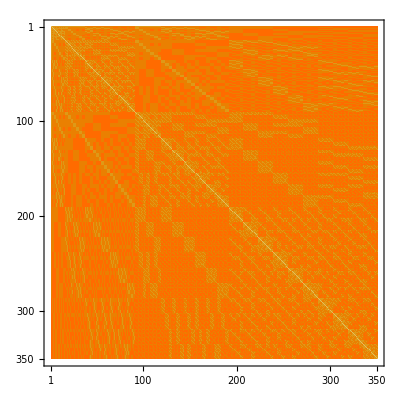

```mathematica
With[
{parts=Select[SetPartitions[7],Length[#]==4&]},
MatrixPlot[
Table[
Table[
Length[
PartitionIntersection[i,j
]],{i,parts}]
,{j,parts}
]
]
]
```

```mathematica
With[
{parts=Select[SetPartitions[8],Length[#]==4&]},
MatrixPlot[
Table[
Table[
Length[
PartitionIntersection[i,j
]],{i,parts}]
,{j,parts}
]
]
]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

-Graphics-

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

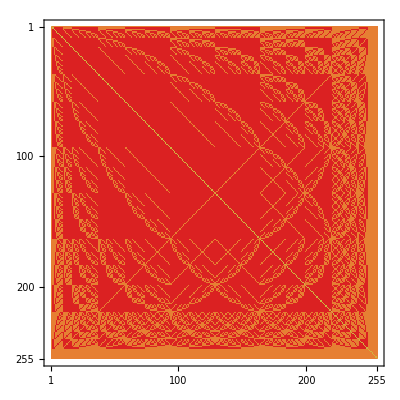

```mathematica
With[
{parts=Sort[Select[SetPartitions[9],Length[#]==2&]]},
MatrixPlot[
Table[
Table[
Length[
PartitionIntersection[i,j
]],{i,parts}]
,{j,parts}
],ColorFunction->"Rainbow"
]
]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

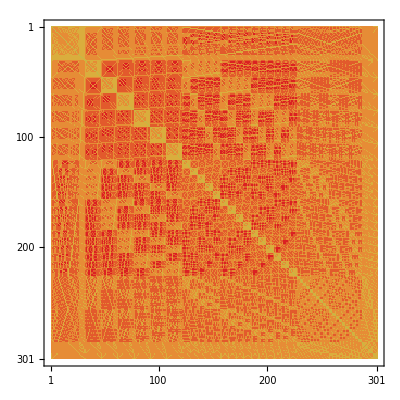

```mathematica
With[
{parts=Sort[Select[SetPartitions[7],Length[#]==3&]]},
MatrixPlot[
Table[
Table[
Length[
PartitionIntersection[i,j
]],{i,parts}]
,{j,parts}
],ColorFunction->"Rainbow"
]
]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

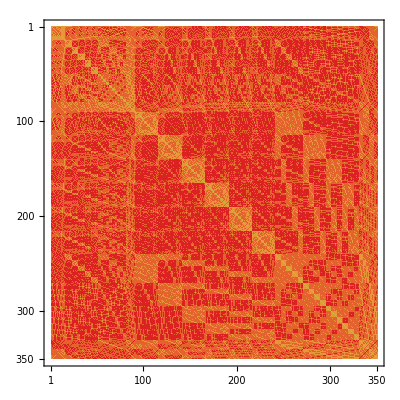

```mathematica
With[
{parts=Sort[Select[SetPartitions[7],Length[#]==4&]]},
MatrixPlot[
Table[
Table[
Length[
PartitionIntersection[i,j
]],{i,parts}]
,{j,parts}
],ColorFunction->"Rainbow"
]
]
```